```mathematica
f[x_]:=s1 Exp[-s2 *x]
```

```mathematica
s1:= 0.0372
```

```mathematica
s2:=0.0007
```

```mathematica
Clear[s]
```

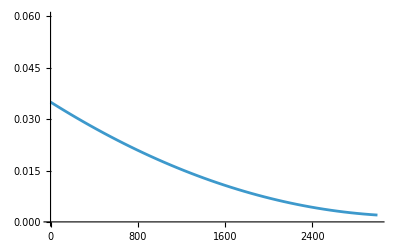

```mathematica
Plot[f[x],{x,0,3000},PlotRange->{0,0.06}]
```

```mathematica
p[T_] := -1/s2*Log[T/s1]
```

```mathematica
μ[T_] := Integrate[x *f[x],{x,0,p[T]}]
```

```mathematica
V[T_] := Simplify[Integrate[x^2*f[x],{x,0,p[T]}]-μ[T]^2]
```

```mathematica
TotalVar[T_] :=p[T]*V[T]+p[T]*(1-p[T])*μ[T]^2
```

```mathematica
Plot[TotalVar[T],{T,0.001,0.06}]
```

-Graphics-

## Example 2: polynomial

```mathematica
f[x_]:=a * x^2+b * x + c
```

```mathematica
Solve[a * x^2+b * x + c==T,x]
```

{{x→(-b-√(b^2-4 a c+4 a T))/(2 a)},{x→(-b+√(b^2-4 a c+4 a T))/(2 a)}}

```mathematica
p[T_]:=(-b-√(b^2-4 a c+4 a T))/(2 a)
```

```mathematica
Clear[a,b,c,T]
```

```mathematica
a:=3*10^-9
```

```mathematica
b:=-2*10^-5
```

```mathematica
c:=0.035
```

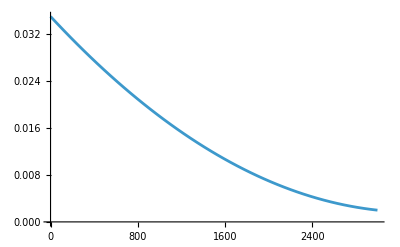

```mathematica
Plot[f[x],{x,0,3000}]
```

```mathematica
μ[T_] := Integrate[x *f[x],{x,0,p[T]}]
```

```mathematica
V[T_] := Simplify[Integrate[x^2*f[x],{x,0,p[T]}]-μ[T]^2]
```

```mathematica
TotalVar[T_] :=p[T]*V[T]+p[T]*(1-p[T])*μ[T]^2
```

```mathematica
Plot[TotalVar[T],{T,0.001,0.06}]
```

-Graphics-

## Example 3: polynomial dg3

```mathematica
f[x_]:=(a * x^3+b * x^2 + c*x+d)
```

```mathematica
Solve[a * x^3+b * x^2 + c*x+d==T,x]
```

{{x→-b/(3 a)-(2^(1/3) (-b^2+3 a c))/(3 a (-2 b^3+9 a b c-27 a^2 d+27 a^2 T+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d+27 a^2 T)^2))^(1/3))+((-2 b^3+9 a b c-27 a^2 d+27 a^2 T+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d+27 a^2 T)^2))^(1/3))/(3 2^(1/3) a)},{x→-b/(3 a)+((1+ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+27 a^2 T+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d+27 a^2 T)^2))^(1/3))-((1-ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+27 a^2 T+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d+27 a^2 T)^2))^(1/3))/(6 2^(1/3) a)},{x→-b/(3 a)+((1-ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+27 a^2 T+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d+27 a^2 T)^2))^(1/3))-((1+ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+27 a^2 T+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d+27 a^2 T)^2))^(1/3))/(6 2^(1/3) a)}}

```mathematica
p[T_]:=-b/(3 a)-(2^(1/3) (-b^2+3 a c))/(3 a (-2 b^3+9 a b c-27 a^2 d+27 a^2 T+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d+27 a^2 T)^2))^(1/3))+((-2 b^3+9 a b c-27 a^2 d+27 a^2 T+√(4 (-b^2+3 a c)^3+(-2 b^3+9 a b c-27 a^2 d+27 a^2 T)^2))^(1/3))/(3 2^(1/3) a)
```

```mathematica
Clear[a,b,c,T]
```

```mathematica
a:=-5*10^-12
```

```mathematica
b:=3*10^-8
```

```mathematica
c:=-6*10^-5
```

```mathematica
d:=0.05
```

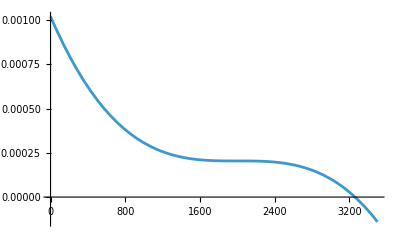

```mathematica
Plot[f[x],{x,0,3500}]
```

```mathematica
μ[T_] := Integrate[x *f[x],{x,0,p[T]}]
```

```mathematica
V[T_] := Simplify[Integrate[x^2*f[x],{x,0,p[T]}]-μ[T]^2]
```

```mathematica
TotalVar[T_] :=p[T]*V[T]+p[T]*(1-p[T])*μ[T]^2
```

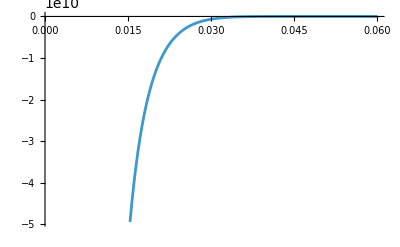

```mathematica
Plot[TotalVar[T],{T,0.001,0.06}]
```